## pixel-based

## fitting

```mathematica
dotSize=21;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
```

```mathematica
dotRatio=0.5;
```

```mathematica
res=Parallelize[Table[
Module[
{image,posList,fillingRatio,fitParam},
image=ConstantArray[0,Round[{dotSize/dotRatio,29 dotSize/dotRatio}]];
posList=Table[{
RandomInteger[Dimensions[image][[1]]],
RandomInteger[Dimensions[image][[2]]]
},{n,1,900}];
fillingRatio=Table[{
n,
N[Length[Select[
DeleteDuplicates[Flatten[Table[Map[pos+#&,dotPoints],{pos,posList[[1;;n]]}],1]],
Between[#[[1]],{1,Dimensions[image][[1]]}]&&
Between[#[[2]],{1,Dimensions[image][[2]]}]
&]]/ProductAcross[Dimensions[image]]]
},{n,1,900,25}];
fitParam=Mean[Flatten[Select[Map[a/.Quiet[Solve[2-(1+Exp[-#[[1]]/a])==#[[2]],a]]&,fillingRatio],Length[#]==1&&NumberQ[#[[1]]]&]]];
{dotRatio,fitParam,fillingRatio}
]
,{dotRatio,0.01,0.3,0.01}]];
```

```mathematica
Transpose[Transpose[res][[1;;2]]]
```

```mathematica
res2={{0.01,366790.19269602123},{0.02,92134.60957369041},{0.03,40968.54612267233},{0.04,22983.5072021985},{0.05,14754.07632907185},{0.06,10409.63096097543},{0.06999999999999999,7628.650384802171},{0.07999999999999999,5860.383374359392},{0.09,4648.177576291479},{0.09999999999999999,3750.165478952977},{0.10999999999999999,3102.742002595605},{0.12,2625.281945233505},{0.13,2244.1743172619867},{0.14,1947.6245222709686},{0.15,1678.3407283804747},{0.16,1474.6223038926241},{0.17,1368.4741582805832},{0.18,1197.2520379850935},{0.19,1060.3575085519938},{0.2,949.3647962982409},{0.21000000000000002,886.9589210517737},{0.22000000000000003,798.308859262075},{0.23,742.7023297771328},{0.24000000000000002,669.8682978799892},{0.25,634.8564318152364},{0.26,570.9294656529814},{0.27,532.965323830488},{0.28,503.1846824141916},{0.29000000000000004,499.8546423218291},{0.30000000000000004,435.3128313772401}};
```

```mathematica
res2fit=NonlinearModelFit[res2,a Exp[b Log[x]]+c,{a,b,c,d},x,MaxIterations->100000];
```

```mathematica
ExponentFitFunction[x_]:=36.1809678369143+37.54838351114363/x^1.9948966301731763
```

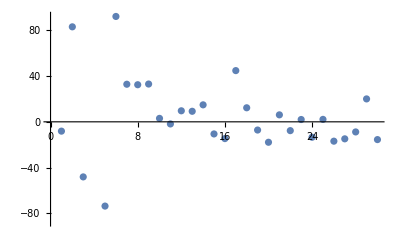

```mathematica
ListPlot[Transpose[Map[
{
#[[1]],
#[[2]],
res2fit[#[[1]]],
#[[2]]-res2fit[#[[1]]]
}
&,res2]][[4]]]
```

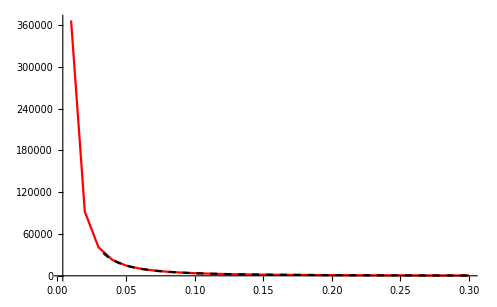

```mathematica
Show[{
ListPlot[res2,Joined->True,PlotRange->All,PlotStyle->Red],
Plot[res2fit[x],{x,0,0.3},PlotStyle->{Dashed,Black}]
}]
```

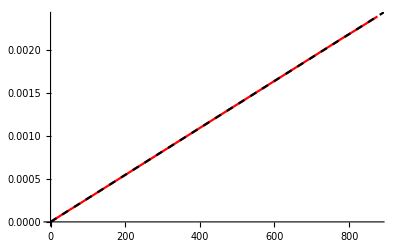

```mathematica
Show[{
ListPlot[
res[[1]][[3]],
Joined->True,PlotRange->{All,All},PlotStyle->Red
],
Plot[
2-(1+Exp[-x/res[[1]][[2]]]),{x,0,900},PlotStyle->{Dashed,Black}
]
}]
```

```mathematica
dotRatio=0.25;
fillingRatio=0.25;
```

```mathematica
HowManyFrames[dotRatio_,fillingRatio_]:=Round[(-37.5484-36.181dotRatio^(1.9948))Log[1-fillingRatio]/dotRatio^(1.9948)]
```

## p5js

```mathematica
(HowManyFrames[dotRatio,fillingRatio]-HowManyFrames[dotRatio,0.1])0.9
```

103.5

```mathematica
?Log
```

```mathematica
Log[6]//N
```

1.79176

```mathematica
alma=Round[ImageData[Import[NotebookDirectory[]<>"test.png"]]];
Length[Select[Flatten[alma,1],#=={0,0,0,1}||#=={0,0,0}&]]/Length[Flatten[alma,1]]//N
```

0.252829

```mathematica
(0.28754630948988313+0.15844970076944997)/2
```

0.222998

```mathematica
53
```

```mathematica
HowManyFrames[0.5,0.25]
```

53

```mathematica
0.04547563805104404 0.2521268368136118 0.2521268368136118 9 40 0 49
```

```mathematica
HowManyFrames[0.5,0.04547563805104404]
```

9

```mathematica
HowManyFrames[0.5,0.2521268368136118]
```

54

```mathematica
korte=Round[ImageData[Import[NotebookDirectory[]<>"result.png"]]];
```

```mathematica
korte//Dimensions
```

{1079,1079,4}

```mathematica
Ceiling[1079/29]
```

```mathematica
38
```

```mathematica
N[Length[Position[Flatten[korte[[-38;;-1]],1],{0,0,0,1}]]/(1079 38)]
```

0.243013

```mathematica
N[Length[Position[Flatten[Transpose[Transpose[korte][[-38;;-1]]],1],{0,0,0,1}]]/(1079 38)]
```

0.252085

## Mathematica

### functions

```mathematica
MinPos[list_]:=Flatten[Position[list,Min[list]]][[1]]
```

```mathematica
ImageMatrixFromBlackPixels[pixels_,w_,h_]:=Normal[SparseArray[Map[#->0&,pixels],{w,h},1]]
```

```mathematica
InvertMatrix[matrix_]:=matrix/.{0->1,1->0}
```

```mathematica
PutBlackPixelsInOrder[blackPixels_,validPositions_]:=Module[
{blackPixelsLocal},
blackPixelsLocal=DeleteDuplicates[blackPixels]∩validPositions;
{
blackPixelsLocal,
N[Length[blackPixelsLocal]/Length[validPositions]]
}
]
```

```mathematica
FillingRatioRegions[image_]:=N[1-Mean[Flatten[{
Table[
image[[
n 4pixelSize sW+1;;(n 4+1)pixelSize sW,
1;;pixelSize
]]
,{n,0,7}],
Table[Table[
image[[
(4n+1)pixelSize sW+1;;(4n+4)pixelSize sW,
m 4pixelSize sW+1;;(m 4+1)pixelSize sW
]],{n,0,6}],{m,0,7}]
}]]]
```

```mathematica
RGBLinearize[rgbCol_]:=Map[
If[
#<=0.04045,
#/12.92,
Power[(#+0.055)/1.055,2.4]
]
&,rgbCol]
LinearRGBToLuminance[linearRgbCol_]:={0.2126,0.7152,0.0722}.linearRgbCol
LuminanceToPerceivedLightness[luminance_]:=If[
luminance<=216/24389,
luminance (24389/27),
Power[luminance,1/3]116-16
]
Luminance[rgbCol_]:=LuminanceToPerceivedLightness[LinearRGBToLuminance[RGBLinearize[rgbCol]]]/100
```

```mathematica
RGBLinearize[rgbCol_]:=Map[
Power[(#+0.055)/1.055,2.4]
&,rgbCol]
LinearRGBToLuminance[linearRgbCol_]:={0.2126,0.7152,0.0722}.linearRgbCol
LuminanceToPerceivedLightness[luminance_]:=Power[luminance,1/3]116-16
Luminance[rgbCol_]:=LuminanceToPerceivedLightness[LinearRGBToLuminance[RGBLinearize[rgbCol]]]/100
```

```mathematica
TriangularPosition[rgbCol_]:=Map[rgbCol.#&,Transpose[{{0,1},{-(√3)/2,-1/2},{(√3)/2,-1/2}}]]
```

```mathematica
TriangularPosition3D[rgbCol_]:=Flatten[{Map[rgbCol.#&,Transpose[{{0,1},{-(√3)/2,-1/2},{(√3)/2,-1/2}}]],Luminance[rgbCol]}]
```

```mathematica
IsoluminancePlot[rgbCols_,pointSize_]:=Graphics[{
White,EdgeForm[Black],
Polygon[
Table[
{Cos[a+Pi/2],Sin[a+Pi/2]}
,{a,0,2Pi-2Pi/6,2Pi/6}]
],
Map[{
EdgeForm[RGBColor[#]],RGBColor[#],Rectangle[TriangularPosition[#]-pointSize/2,TriangularPosition[#]+pointSize/2]
}&,rgbCols]
}]

IsoluminancePlot3D[rgbCols_,pointSize_]:=Graphics3D[{
PointSize->pointSize,
Map[{
RGBColor[#],Point[TriangularPosition3D[#]]
}&,rgbCols],
PointSize->2 pointSize,Map[{
RGBColor[#],Point[TriangularPosition3D[#]]
}&,{
{0,0,0},
{1,0,0},
{0,1,0},
{0,0,1},
{1,1,0},
{0,1,1},
{1,0,1},
{1,1,1}
}]
}]
```

```mathematica
AllBetweenRange[list_,range_]:=Total[Boole[Map[Between[#,range]&,list]]]/Length[list]==1
```

```mathematica
GetVerticalStreets[image_]:=Module[
{spans},
spans=Table[Map[Round,{
1,pixelSize,
n 4pixelSize sW+1,(n 4+1)pixelSize sW 
}],{n,0,7}];
Table[
image[[span[[1]];;span[[2]],span[[3]];;span[[4]]]],
{span,spans}]
]
```

```mathematica
GetHorizontalStreets[image_]:=Module[
{spans},
spans=Table[Map[Round,{
n 4pixelSize sW+1,(n 4+1)pixelSize sW ,
1,pixelSize
}],{n,0,7}];
Table[
image[[span[[1]];;span[[2]],span[[3]];;span[[4]]]],
{span,spans}]
]
```

```mathematica
MeasureFillingRatio[imagePart_]:=N[1-Mean[Floor[Flatten[imagePart]]]]
```

### startup

```mathematica
n=7;
r=1/3;
approxSize=2000;

bW=1/(n+r+n r);
sW=r bW;
coords=Table[0.5sW+(i-1)(sW+bW),{i,1,n+1}];

possibleSizes=DeleteCases[
Table[
If[(n+1)Round[sW pixelSize]+n Round[bW pixelSize]==pixelSize,pixelSize]
,{pixelSize,approxSize-2n,approxSize+2n}]
,Null];

pixelSize=possibleSizes[[MinPos[
Map[
Abs[approxSize-#]&,
possibleSizes
]]]];

pixelCoords =Flatten[ Table[Table[
If[i==3&&j==3,
{-100,-100},
{Round[coords[[i]] pixelSize,0.5],Round[coords[[j]] pixelSize,0.5]}
]
,{j,2,n}],{i,2,n}],1];
```

```mathematica
gridMatrix=Import[NotebookDirectory[]<>"grid_matrix_2000px.mx"];
```

```mathematica
validPositions=Position[gridMatrix,1];
invalidPositions=Position[gridMatrix,0];
```

### HG generation

```mathematica
maxPossibleDistance=Sqrt[2Power[pixelSize(sW+bW)/2,2]];
```

```mathematica
AbsoluteTiming[gridMatrix=Parallelize[Table[Table[
If[
Total[Table[If[Abs[i pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ||
Total[Table[If[Abs[j pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ,
1,
0
]
,{j,1/pixelSize,1,1/pixelSize}],{i,1/pixelSize,1,1/pixelSize}]];]
```

{46.0255,Null}

```mathematica
Export[NotebookDirectory[]<>"grid_matrix_2030px.mx",gridMatrix];
```

```mathematica
Image[gridMatrix]
```

-Graphics-

### fit

#### find filling parameter for given dot ratio

```mathematica
fillingParamList=Table[dotSize=pixelSize sW dotRatio;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<=dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
iterNum=HowManyFrames[dotRatio,0.8];
checkMod=200;
fitParams=Parallelize[Table[
blackPixels={};
filling=Table[
blackPixels=Join[blackPixels,ConstantArray[RandomSample[validPositions,1][[1]],Length[dotPoints]]+dotPoints];
If[Mod[n,checkMod]==0,
{
blackPixels=Intersection[
DeleteDuplicates[blackPixels],
validPositions
];
{
n,
N[Length[blackPixels]/Length[validPositions]]
}
}
]
,{n,1,iterNum}];
filling=Flatten[DeleteCases[filling,Null],1];
fitParam=Mean[Flatten[Select[Map[a/.Quiet[Solve[2-(1+Exp[-#[[1]]/a])==#[[2]],a]]&,filling],Length[#]==1&&NumberQ[#[[1]]]&]]];
fitParam
,{n,1,10}]];
{
dotRatio,
Mean[fitParams]
},{dotRatio,{0.25,0.5,0.75,1}}];
```

#### sweep

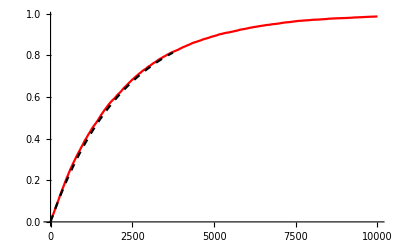

```mathematica
Show[{
ListPlot[
filling,
Joined->True,PlotRange->{All,All},PlotStyle->Red
],
Plot[
2-(1+Exp[-x/fitParam]),{x,0,iterNum},PlotStyle->{Dashed,Black}
]
}]
```

```mathematica
fitParams
```

{2140.63,2134.6,2164.26,2116.26,2141.12,2131.45,2129.04,2123.54,2127.24,2141.43}

```mathematica
sweep=Table[
dotSize=pixelSize sW dotRatio;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<=dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
iterNum=iterNum=HowManyFrames[dotRatio,0.8];
checkMod=50;
fitParams=Parallelize[Table[
blackPixels={};
filling=Table[
blackPixels=Join[blackPixels,ConstantArray[RandomSample[validPositions,1][[1]],Length[dotPoints]]+dotPoints];
If[Mod[n,checkMod]==0,
{
blackPixels=Intersection[
DeleteDuplicates[blackPixels],
validPositions
];
{
n,
N[Length[blackPixels]/Length[validPositions]]
}
}
]
,{n,1,iterNum}];
filling=Flatten[DeleteCases[filling,Null],1];
fitParam=Mean[Flatten[Select[Map[a/.Quiet[Solve[2-(1+Exp[-#[[1]]/a])==#[[2]],a]]&,filling],Length[#]==1&&NumberQ[#[[1]]]&]]];
fitParam
,{n,1,10}]];
{
dotRatio,
Mean[fitParams]
}
,{dotRatio,0.15,1,0.05}];
```

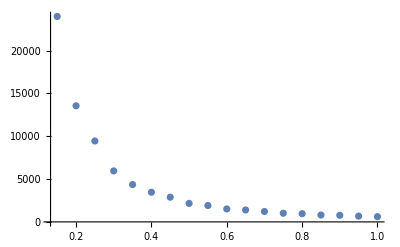

```mathematica
ListPlot[
sweep,PlotRange->All,Joined->False
]
```

```mathematica
sweepFit=NonlinearModelFit[sweep,a Exp[b Log[x]]+c,{a,b,c,d},x,MaxIterations->100000];
```

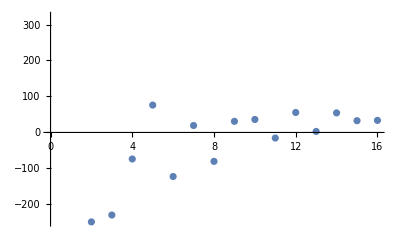

```mathematica
ListPlot[Transpose[Map[
{
#[[1]],
#[[2]],
sweepFit[#[[1]]],
#[[2]]-sweepFit[#[[1]]]
}
&,Drop[Transpose[Transpose[sweep][[{1,2}]]],2]]][[4]]]
```

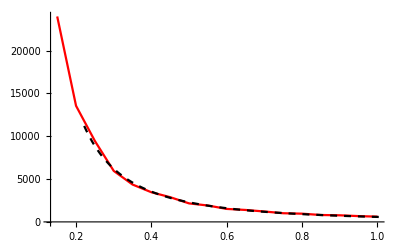

```mathematica
Show[{
ListPlot[sweep,Joined->True,PlotRange->All,PlotStyle->Red],
Plot[sweepFit[x],{x,0,2},PlotStyle->{Dashed,Black}]
}]
```

```mathematica
Clear[dotRatio,fillingRatio]
```

```mathematica
frameNum/.Solve[2-(1+Exp[-frameNum/sweepFit[dotRatio]])==fillingRatio,frameNum][[1]][[1]]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

((-594.553+14.383 dotRatio^1.9497766872687) Log[1.-1. fillingRatio])/dotRatio^1.9497766872687

```mathematica
HowManyFrames[0.25,0.25]
```

2548.48

```mathematica
HowManyFrames[0.25,0.25]
```

2544.

```mathematica
HowManyFrames[dotRatio_,fillingRatio_]:=((-594.5531167303602+14.382988202706352 dotRatio^(1.94977668726869635129617108759703114629`15.954589770191005)) Log[1.`15.954589770191005-1.`15.954589770191005 fillingRatio])/dotRatio^(1.94977668726869635129617108759703114629`15.954589770191005)
```

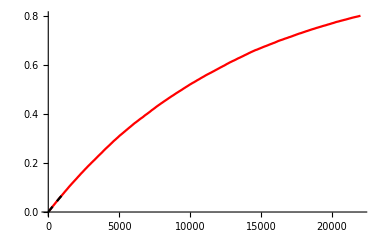

```mathematica
Show[{
ListPlot[
filling,
Joined->True,PlotRange->{All,All},PlotStyle->Red
],
Plot[
2-(1+Exp[-x/fitParam]),{x,0,iterNum},PlotStyle->{Dashed,Black}
]
}]
```

### filling

#### find optimal algorithm

```mathematica
fillingParamList={{0.25,9456.07300836962},{0.5,2149.4655005018235},{0.75,1014.7230418828101},{1,603.653334929545}};
```

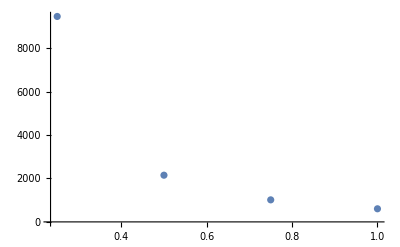

```mathematica
ListPlot[fillingParamList]
```

```mathematica
fillingParam=600;
fillingAim=0.5;
```

```mathematica
exponentSweep=Quiet[Parallelize[Table[GetMeanAndSD[Table[
fillingRatio=0;
lastKnownFillingRatio=fillingAim 0.1;
fillingGo=True;
fillingCharacteristics=Table[
If[fillingGo,
If[
RandomReal[]<Abs[lastKnownFillingRatio^checkExponent],
{
n,
fillingRatio+=N[Evaluate[D[2-(1+Exp[-x/fillingParam]),x]]/.{x->n}],
0.0121961074,
0,
fillingGo,
lastKnownFillingRatio
},
{
n,
fillingRatio+=N[Evaluate[D[2-(1+Exp[-x/fillingParam]),x]]/.{x->n}],
0.0121961074,
0.24275709099999992,
{If[fillingAim<lastKnownFillingRatio,fillingGo=False],fillingGo}[[2]],
{lastKnownFillingRatio=fillingRatio;,lastKnownFillingRatio}[[2]]
}
],
Nothing]
,{n,1,10fillingParam}];
iterStop=Position[fillingCharacteristics,False][[1]][[1]];
{
checkExponent,
Total[Transpose[fillingCharacteristics[[1;;iterStop]]][[3]]]/3600,
Total[Transpose[fillingCharacteristics[[1;;iterStop]]][[4]]]/3600,
(fillingCharacteristics[[iterStop]][[2]]-fillingAim)/fillingAim
},{rep,1,200}]]
,{checkExponent,0.01,1,0.01}]]];
```

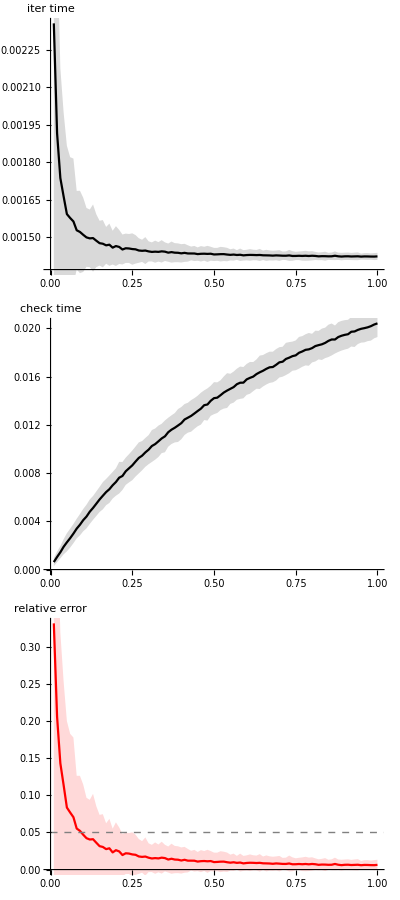

```mathematica
Column[Table[
ErrorListPlot[
{Transpose[Map[{
Transpose[#][[1]][[1]],
Transpose[#][[n]][[1]],
2Transpose[#][[n]][[2]]
}&,exponentSweep]]},
{{Black,Black,Red}[[n-1]]},
{
AxesLabel->{None,{"iter time","check time","relative\nerror"}[[n-1]]},PlotRange->{{All,All},{All,All},{All,All}}[[n-1]],
AspectRatio->0.5,
ImageSize->300,
Epilog->{{},{},{Gray,Dashed,Line[{{0,0.05},{100,0.05}}]}}[[n-1]]
},
{True,True,False}
],{n,2,4}]]
```

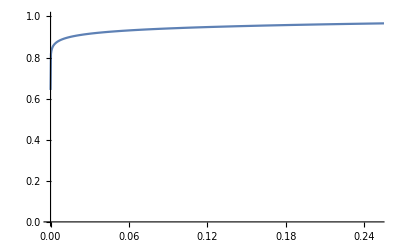

```mathematica
Plot[x^0.025,{x,0,1},PlotRange->{{0,0.25},{0,1}}]
```

ki kell próbálni, hogy implementálva valóban ezt adja-e

#### filling with optimal algorithm

```mathematica
CheckFillingProbability[lastKnownFillingRatio_,fillingAim_,checkExponent_,checkIntercept_,checkInterceptScaling_]:=
Quiet[checkIntercept(1-fillingAim checkInterceptScaling)+ Power[(lastKnownFillingRatio/fillingAim),checkExponent]]
```

##### whole

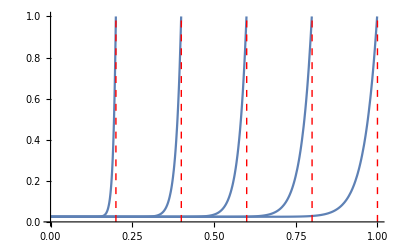

```mathematica
checkExponent=25;
checkIntercept=0.025;
checkInterceptScaling=0;
Plot[
Table[
CheckFillingProbability[lastKnownFillingRatio,fillingAim,checkExponent,checkIntercept,checkInterceptScaling]
,{fillingAim,0.2,1,0.2}],{lastKnownFillingRatio,0,1},
PlotRange->{{0,1},{0,1}},
Epilog->{
Red,Dashed,
Table[
Line[{{fillingAim,0},{fillingAim,1}}]
,{fillingAim,0.2,1,0.2}]
}
]
```

```mathematica
dotRatio=0.5;
fillingAim=0.25;

dotSize=pixelSize sW dotRatio;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<=dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];
image=gridMatrix;
lastKnownFillingRatio=0;
AbsoluteTiming[
While[
lastKnownFillingRatio<fillingAim,
If[
CheckFillingProbability[lastKnownFillingRatio,fillingAim,checkExponent,checkIntercept,checkInterceptScaling]<RandomReal[],
{
Map[
image[[#[[1]]]][[#[[2]]]]=0;
&,Clip[ConstantArray[RandomSample[validPositions,1][[1]],Length[dotPoints]]+dotPoints,{1,pixelSize}]];
},
{
Map[
image[[#[[1]]]][[#[[2]]]]=0;
&,Clip[ConstantArray[RandomSample[validPositions,1][[1]],Length[dotPoints]]+dotPoints,{1,pixelSize}]];
lastKnownFillingRatio=FillingRatioRegions[image];
Echo[ToString[lastKnownFillingRatio/fillingAim]<>"\t"<>ToString[CheckFillingProbability[lastKnownFillingRatio,fillingAim,checkExponent,checkIntercept,checkInterceptScaling]]];
}
]
]][[1]] 
FillingRatioRegions[image]
FillingRatioRegions[image]/fillingAim
Image[image,ImageSize->500]
```

0.0550851	0.025

0.140458	0.025

0.18632	0.025

0.211014	0.025

0.31645	0.025

0.351913	0.025

0.410107	0.025

0.435339	0.025

0.515986	0.0250001

0.564419	0.0250006

0.572978	0.0250009

0.604988	0.0250035

0.610649	0.0250044

0.717438	0.0252481

0.726589	0.0253406

0.753798	0.0258538

0.835362	0.0361397

0.850162	0.0422798

0.852497	0.0435066

0.858551	0.0470876

0.861017	0.0487295

0.874291	0.0597858

0.876175	0.0617091

0.9105	0.12094

0.92569	0.170091

0.929643	0.1864

0.93066	0.190871

0.936389	0.21838

0.940979	0.243522

0.942901	0.254958

0.943571	0.259078

0.949815	0.301043

0.958427	0.370918

0.967274	0.460245

0.967891	0.467246

0.96975	0.488976

0.971443	0.509655

0.975911	0.568563

0.980552	0.637027

0.989721	0.797353

0.991533	0.833505

0.992478	0.852994

0.994098	0.88744

0.994675	0.900055

0.995402	0.91618

0.997379	0.961488

0.999049	1.00148

1.00102	1.05094

5.24836

0.250256

1.00102

-Graphics-

##### in parts

```mathematica
parts=Join[
Table[{
{1,pixelSize},
{n 4pixelSize sW+1,(n 4+1)pixelSize sW }
},{n,0,7}],
Table[{
{n 4pixelSize sW+1,(n 4+1)pixelSize sW },
{1,pixelSize}
},{n,0,7}]
];
```

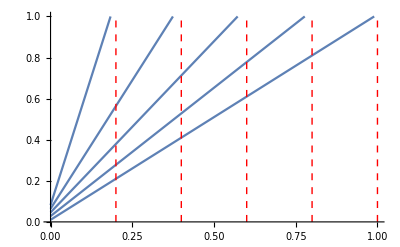

```mathematica
checkExponent=1;
checkIntercept=0.1;
checkInterceptScaling=0.9;
Plot[
Table[
CheckFillingProbability[lastKnownFillingRatio,fillingAim,checkExponent,checkIntercept,checkInterceptScaling]
,{fillingAim,0.2,1,0.2}],{lastKnownFillingRatio,0,1},
PlotRange->{{0,1},{0,1}},
Epilog->{
Red,Dashed,
Table[
Line[{{fillingAim,0},{fillingAim,1}}]
,{fillingAim,0.2,1,0.2}]
}
]
```

```mathematica
Table[Table[
dotSize=pixelSize sW dotRatio;
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<=dotSize/2,
{i,j},
Nothing
]
,{j,Floor[-dotSize/2],Ceiling[dotSize/2]}],{i,Floor[-dotSize/2],Ceiling[dotSize/2]}],1];

dotPointsLength=Length[dotPoints];
dotPointsTransposed=Transpose[dotPoints];

image=gridMatrix;
fillingCharacteristics=Table[
vFrom=part[[1]][[1]];
vTo=part[[1]][[2]] ;
hFrom=part[[2]][[1]];
hTo=part[[2]][[2]];

lastKnownFillingRatio=N[1-Mean[Flatten[image[[vFrom;;vTo,hFrom;;hTo]]]]];
{
AbsoluteTiming[
While[
lastKnownFillingRatio<fillingAim,
If[
CheckFillingProbability[lastKnownFillingRatio,fillingAim,checkExponent,checkIntercept,checkInterceptScaling]<RandomReal[],
{
Map[
image[[Clip[#[[1]],{vFrom,vTo}]]][[Clip[#[[2]],{hFrom,hTo}]]]=0.25;&,
ConstantArray[{RandomInteger[{vFrom,vTo}],RandomInteger[{hFrom,hTo}]},dotPointsLength]+dotPoints
];
},
{
Map[
image[[Clip[#[[1]],{vFrom,vTo}]]][[Clip[#[[2]],{hFrom,hTo}]]]=0.25;&,
ConstantArray[{RandomInteger[{vFrom,vTo}],RandomInteger[{hFrom,hTo}]},dotPointsLength]+dotPoints
];
lastKnownFillingRatio=N[1-Mean[Round[Flatten[image[[vFrom;;vTo,hFrom;;hTo]]]]]]
}
]
]][[1]] ,
N[1-Mean[Round[Flatten[image[[vFrom;;vTo,hFrom;;hTo]]]]]],
N[1-Mean[Round[Flatten[image[[vFrom;;vTo,hFrom;;hTo]]]]]]/fillingAim
},
{part,parts}];
Export[NotebookDirectory[]<>"grids\\dot_ratio_"<>ToString[dotRatio]<>"_filling_ratio_"<>ToString[fillingAim]<>".png",Image[image]];
,{dotRatio,{0.2,0.25,0.4,0.5,0.75,1,2}}],{fillingAim,{0.25,0.5}}];
```

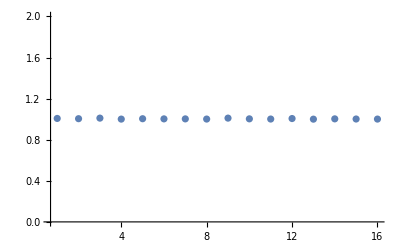

```mathematica
ListPlot[Transpose[fillingCharacteristics][[3]],PlotRange->{All,{0,2}}]
```

#### patterned filling

```mathematica
noiseLevel=0;
ampRatio=0;
dotRatio=Sqrt[2];
dotFreq=1;
```

```mathematica
Table[
dotSize=Round[0.5dotRatio pixelSize sW ];
dotPoints=Flatten[Table[Table[
If[
EuclideanDistance[{0,0},{i,j}]<=dotSize,
{i,j},
Nothing
]
,{j,-dotSize,dotSize}],{i,-dotSize,dotSize}],1];
dotPointsNum=Length[dotPoints];
Table[
Table[
Table[
dotSizeString="dot_size_"<>ToString[N[dotRatio/Sqrt[2]]]<>"(sqrt2)";
noiseString="noise_"<>ToString[noiseLevel];
dotFreqString="dot_freq_"<>ToString[dotFreq];
ampString="amp_"<>ToString[ampRatio];
runString=StringRiffle[{dotSizeString,noiseString,dotFreqString,ampString},"_"];
saveString=StringRiffle[{noiseString,dotFreqString,ampString},"\\"]<>"\\"<>dotSizeString;

freq=1;
parallelPlacementNoiseMaxRatio=4 noiseLevel;
perpendicularPlacementNoiseMaxRatio=1.5 noiseLevel;


amp=Round[ampRatio pixelSize sW];
parallelPlacementNoiseMax=Round[parallelPlacementNoiseMaxRatio pixelSize sW];
perpendicularPlacementNoiseMax=Round[perpendicularPlacementNoiseMaxRatio pixelSize sW];

padding=Round[(4+Sqrt[2] 2) pixelSize sW];
xDotFreq=dotFreq;
yDotFreq=dotFreq;
xFreq=freq;
xAmp=amp;
yFreq=freq;
yAmp=-amp;
dotNum=Length[Range[1,1/sW,dotFreq]](n+1)+(Length[Range[1,1/sW,dotFreq]]-(n+1))(n+1);

image=ArrayPad[gridMatrix,padding,1];
streetMiddlePoint=Ceiling[sW pixelSize 0.5];
Table[Table[
perpendicularPlacementNoise=RandomReal[{-perpendicularPlacementNoiseMax,perpendicularPlacementNoiseMax}/2];
parallelPlacementNoise=RandomReal[{-parallelPlacementNoiseMax,parallelPlacementNoiseMax}/2];
hPos=padding+Round[n sW pixelSize+streetMiddlePoint+xAmp Sin[2Pi m/4 xFreq]+perpendicularPlacementNoise];
vPos=padding+Round[m sW pixelSize+streetMiddlePoint+parallelPlacementNoise];
Map[
Quiet[If[image[[hPos+#[[1]]]][[vPos+#[[2]]]]!=0,image[[hPos+#[[1]]]][[vPos+#[[2]]]]=0.5;]]
&,dotPoints]
,{m,0,1/sW-1,xDotFreq}],{n,0,1/sW-1,4}];
Table[Table[
perpendicularPlacementNoise=RandomReal[{-perpendicularPlacementNoiseMax,perpendicularPlacementNoiseMax}/2];
parallelPlacementNoise=RandomReal[{-parallelPlacementNoiseMax,parallelPlacementNoiseMax}/2];
hPos=padding+Round[n sW pixelSize+streetMiddlePoint+parallelPlacementNoise];
vPos=padding+Round[m sW pixelSize+streetMiddlePoint+yAmp Sin[2Pi n/4yFreq]+perpendicularPlacementNoise];
Map[
Quiet[If[image[[hPos+#[[1]]]][[vPos+#[[2]]]]!=0,image[[hPos+#[[1]]]][[vPos+#[[2]]]]=0.5;]]
&,dotPoints]
,{m,0,1/sW-1,4}],{n,0,1/sW-1,yDotFreq}];
Export[
NotebookDirectory[]<>"grids\\regular\\sweep\\"<>saveString<>".png",Image[image]
];
Echo[runString];
,{noiseLevel,0,1,0.25}]
,{ampRatio,{0,0.25,0.5}}]
,{dotFreq,{0.5,1,2,4}}]
,{dotRatio,0,Sqrt[2],Sqrt[2]/10}];
```

```mathematica
dotSizeString="dot_size_"<>ToString[N[dotRatio/Sqrt[2]]]<>"(sqrt2)";
noiseString="noise_"<>ToString[noiseLevel];
dotFreqString="dot_freq_"<>ToString[dotFreq];
ampString="amp_"<>ToString[ampRatio];
runString=StringRiffle[{dotSizeString,noiseString,dotFreqString,ampString},"_"]
```

dot_size_1.(sqrt2)_noise_0_dot_freq_1_amp_0

noise_0\dot_freq_1\amp_0\dot_size_1.(sqrt2)

```mathematica
Mean[Flatten[{Map[MeasureFillingRatio,GetHorizontalStreets[ArrayPad[image,-padding]]],Map[MeasureFillingRatio,GetVerticalStreets[ArrayPad[image,-padding]]]}]]
```

0.759384

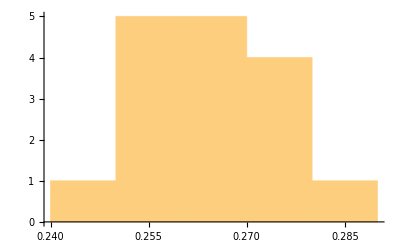

```mathematica
Histogram[Flatten[{Map[MeasureFillingRatio,GetHorizontalStreets[ArrayPad[image,-padding]]],Map[MeasureFillingRatio,GetVerticalStreets[ArrayPad[image,-padding]]]}]]
```

```mathematica
N[Length[Position[ArrayPad[image,-padding],0.5]]/Length[Position[gridMatrix,1]]]
```

0.173819

```mathematica
N[Length[Position[ArrayPad[image,-padding],0.5]]/Length[Position[gridMatrix,1]]]/(dotPointsNum dotNum/Length[Position[gridMatrix,1]])
```

0.636794

ha korrigálni szeretnénk az átlapolódásért, akkor a kontrakció gyökével kell szorozni a zaj nélküli esetben a foltméretet ahhoz, hogy azonos legyen a fedés

```mathematica
BackAndForthFrames[frames_]:=Join[frames,Drop[Drop[Reverse[frames],1],-1]]
```

```mathematica
dotRatios=Table[dotRatio,{dotRatio,0,Sqrt[2],Sqrt[2]/10}];
dotFreqs=Table[dotFreq,{dotFreq,{0.5,1,2,4}}]
ampRatios=Table[ampRatio,{ampRatio,{0,0.25,0.5}}]
noiseLevels=Table[noiseLevel,{noiseLevel,0,1,0.25}]
```

{0.5,1,2,4}

{0,0.25,0.5}

{0.,0.25,0.5,0.75,1.}

```mathematica
colorSet1={
{0.7,-0.4,0.4},
{0.7,0.1,-0.5},
{0.6,-0.4,0.4},
{0.8,0.1,-0.5}
};
colorSet2={
{0.7,-0.4,-0.3},
{0.7,0.2,0.2},
{0.6,-0.4,-0.3},
{0.8,0.2,0.2}
};
colorSet3={
{0.7,-0.4,-0.4},
{0.7,-0.4,0.5},
{0.6,-0.4,-0.4},
{0.8,-0.4,0.5}
};
colorSets={colorSet1,colorSet2,colorSet3};
```

```mathematica
isoluminanceLevels=Table[l,{l,0.1,1,0.1}];
```

```mathematica
dotFreq=dotFreqs[[1]];
ampRatio=ampRatios[[2]];
noiseLevel=noiseLevels[[2]];
```

```mathematica
imageDataList=Table[
dotSizeString="dot_size_"<>ToString[N[dotRatio/Sqrt[2]]]<>"(sqrt2)";
noiseString="noise_"<>ToString[noiseLevel];
dotFreqString="dot_freq_"<>ToString[dotFreq];
ampString="amp_"<>ToString[ampRatio];
saveString=StringRiffle[{noiseString,dotFreqString,ampString},"\\"]<>"\\"<>dotSizeString;
Round[ImageData[Import[NotebookDirectory[]<>"grids\\regular\\sweep\\"<>saveString<>".png"]],0.25]
,{dotRatio,dotRatios}];
```

```mathematica
colorSet=3;
l11=colorSets[[colorSet]][[1]][[1]]10;
u11=colorSets[[colorSet]][[1]][[2]];
v11=colorSets[[colorSet]][[1]][[3]];
l12=colorSets[[colorSet]][[2]][[1]]10;
u12=colorSets[[colorSet]][[2]][[2]];
v12=colorSets[[colorSet]][[2]][[3]];
l21=colorSets[[colorSet]][[3]][[1]]10;
u21=colorSets[[colorSet]][[3]][[2]];
v21=colorSets[[colorSet]][[3]][[3]];
l22=colorSets[[colorSet]][[4]][[1]]10;
u22=colorSets[[colorSet]][[4]][[2]];
v22=colorSets[[colorSet]][[4]][[3]];
```

```mathematica
Row[{
Image[
imageDataList[[4]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}],
0.5->LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]
},
ImageSize->400
],
Image[
imageDataList[[4]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}],
0.5->LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]
},
ImageSize->400
]
}]
```

-Graphics--Graphics-

```mathematica
frameList=Map[
Row[{
Image[
#/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}],
0.5->LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]
},
ImageSize->400
],
Image[
#/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}],
0.5->LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]
},
ImageSize->400
]
}]
&,imageDataList
];
```

```mathematica
Export[
NotebookDirectory[]<>"grids\\regular\\sweep\\test_anim.gif",
BackAndForthFrames[frameList],
"DisplayDurations"->ConstantArray[1,Length[BackAndForthFrames[frameList]]]
]
```

C:\Users\marku\Documents\CEU\hermann grid\human\granularity_effect\grids\regular\sweep\test_anim.gif

### isoluminant colors

```mathematica
rgbSpaceLowRes=Table[Table[Table[{r,g,b},{b,0,1,0.1}],{g,0,1,0.1}],{r,0,1,0.1}];
```

```mathematica
IsoluminancePlot3D[Flatten[rgbSpaceLowRes,2]]
```

-Graphics3D-

```mathematica
LUVToRGB[luvColor_]:=Module[
{res},
res=Map[Re,{r,g,b}/.Quiet[FindRoot[
Map[#[[1]]==#[[2]]&,Transpose[{TriangularPosition3D[{r,g,b}],{luvColor[[2]],luvColor[[3]],luvColor[[1]]}}]],
{{r,1},{g,1},{b,1}}
]]];
If[AllBetweenRange[res,{0,1}],res,{0,0,0}]
]
```

```mathematica
luvSpaceRes=0.5;
```

```mathematica
luvColorSpace=Parallelize[Table[Table[Table[
LUVToRGB[{l,u,v}]
,{v,-2,2,luvSpaceRes}],{u,-2,2,luvSpaceRes}],{l,0,1,luvSpaceRes}]];
```

```mathematica
IsoluminancePlot3D[Flatten[luvColorSpace,2]]
```

-Graphics3D-

```mathematica
Manipulate[
IsoluminancePlot3D[{LUVToRGB[{l,u,v}]}],
{{l,0.5},0,1,0.05},
{{u,0},-1,1,0.05},
{{v,0},-1,1,0.05}
]
```

### heterochromatic flicker photometry

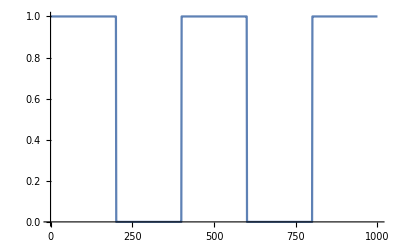

```mathematica
freq=5;
ListPlot[
Table[
Round[0.5+Sin[Pi millis freq/1000]/2]
,{millis,1,1000}],
Joined->True
]
```

```mathematica
luvSpaceRes=0.05;
```

```mathematica
LUVToRGBLookupTable=Flatten[Parallelize[Table[Table[Table[
{{l,u,v},LUVToRGB[{l,u,v}]}
,{v,-2,2,luvSpaceRes}],{u,-2,2,luvSpaceRes}],{l,0,1,luvSpaceRes}]],2];
```

```mathematica
Export[NotebookDirectory[]<>"LUV2RGB_lookup.csv",LUVToRGBLookupTable];
```

```mathematica
Select[
LUVToRGBLookupTable,
#[[1]][[1]]==0.5&&#[[1]][[2]]==0.5
&
][[1]][[1]][[3]]
```

{{0.5,0.5,-2.},{0,0,0}}

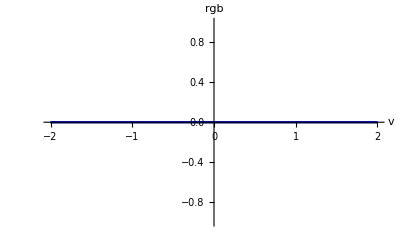
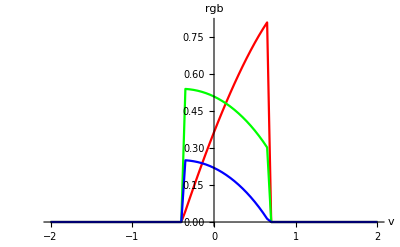
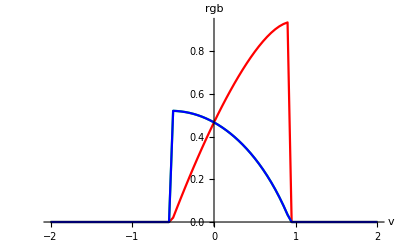
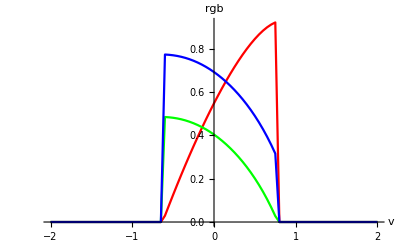
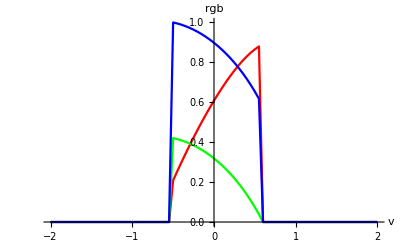
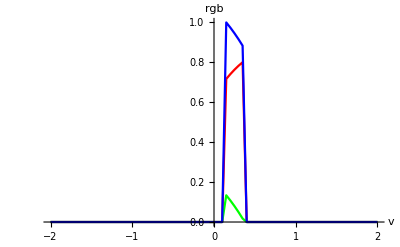
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
l=0.5;
u=0.5;
Table[ListPlot[
Transpose[
Map[
{
{
#[[1]][[3]],
#[[2]][[1]]
},
{
#[[1]][[3]],
#[[2]][[2]]
},
{
#[[1]][[3]],
#[[2]][[3]]
}
}&,
Select[
LUVToRGBLookupTable,
#[[1]][[1]]==l&&#[[1]][[2]]==u
&
]
]],
Joined->True,PlotStyle->{Red,Green,Blue},
AxesLabel->{"v","rgb"}
],{u,-2,2,0.25}]
```

## applet 1

```mathematica
images=Table[Table[
Round[ImageData[Import[NotebookDirectory[]<>"grids\\dot_ratio_"<>ToString[dotRatio]<>"_filling_ratio_"<>ToString[fillingAim]<>".png"]],0.25]
,{dotRatio,{0.2,0.25,0.4,0.5,0.75,1,2}}],{fillingAim,{0.25,0.5}}];
```

```mathematica
isoluminancePlots=Table[
IsoluminancePlot[
DeleteCases[
Flatten[
Table[Table[LUVToRGB[{l,u,v}],{v,-1,1,0.1}],{u,-1,1,0.1}],
1],
{0,0,0}],
0.1
]
,{l,0.1,1,0.1}];
```

```mathematica
isoluminanceLevels=Table[l,{l,0.1,1,0.1}];
```

```mathematica
colorSet1={
{0.7,-0.4,0.4},
{0.7,0.1,-0.5},
{0.6,-0.4,0.4},
{0.8,0.1,-0.5}
};
```

```mathematica
colorSet2={
{0.7,-0.4,-0.3},
{0.7,0.2,0.2},
{0.6,-0.4,-0.3},
{0.8,0.2,0.2}
};
```

```mathematica
colorSet3={
{0.7,-0.4,-0.4},
{0.7,-0.4,0.5},
{0.6,-0.4,-0.4},
{0.8,-0.4,0.5}
};
```

```mathematica
size=410;
colorSelectorFactor=0.3;
colorSet=colorSet3;
Manipulate[
Row[{
Column[{
Show[{
isoluminancePlots[[l11]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}]],EdgeForm[{Thick,Black}],Ellipsoid[{u11,v11},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor],
Show[{
isoluminancePlots[[l12]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]],EdgeForm[{Thick,Black}],Ellipsoid[{u12,v12},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor]
},"\n"],
Image[
images[[fillingAim]][[dotRatio]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}],
0.25->LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]
},
ImageSize->size
],
Image[
images[[fillingAim]][[dotRatio]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}],
0.25->LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]
},
ImageSize->size
],
Column[{
Show[{
isoluminancePlots[[l21]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}]],EdgeForm[{Thick,Black}],Ellipsoid[{u21,v21},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor],
Show[{
isoluminancePlots[[l22]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]],EdgeForm[{Thick,Black}],Ellipsoid[{u22,v22},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor]
},"\n"]
}," "],
{{dotRatio,4},Map[#[[1]]->#[[2]]&,Transpose[{Range[7],{0.2,0.25,0.4,0.5,0.75,1,2}}]]},
{{fillingAim,2},Map[#[[1]]->#[[2]]&,Transpose[{Range[2],{0.25,0.5}}]]},

{{l11,colorSet[[1]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u11,colorSet[[1]][[2]]},-1,1,0.1},
{{v11,colorSet[[1]][[3]]},-1,1,0.1},
{{l12,colorSet[[2]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u12,colorSet[[2]][[2]]},-1,1,0.1},
{{v12,colorSet[[2]][[3]]},-1,1,0.1},
{{l21,colorSet[[3]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u21,colorSet[[3]][[2]]},-1,1,0.1},
{{v21,colorSet[[3]][[3]]},-1,1,0.1},
{{l22,colorSet[[4]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u22,colorSet[[4]][[2]]},-1,1,0.1},
{{v22,colorSet[[4]][[3]]},-1,1,0.1},
ControlPlacement->Top
]
```

```mathematica
(*

legyen skála a rendezettségre is: szinuszosan elhelyezett foltok, egyre több pozicionális zajjal;

jó a teljes grides kitöltés, de legyen megmutatva a hisztogram a kitöltöttségi zajra

*)
```

## applet 2

```mathematica
images=Table[Table[Table[Table[
dotSizeString="dot_size_"<>ToString[N[dotRatio/Sqrt[2]]]<>"(sqrt2)";
noiseString="noise_"<>ToString[noiseLevel];
dotFreqString="dot_freq_"<>ToString[dotFreq];
ampString="amp_"<>ToString[ampRatio];
saveString=StringRiffle[{noiseString,dotFreqString,ampString},"\\"]<>"\\"<>dotSizeString;
Round[ImageData[Import[NotebookDirectory[]<>"grids\\regular\\sweep\\"<>saveString<>".png"]],0.25]
,{noiseLevel,0,1,0.25}]
,{ampRatio,{0,0.25,0.5}}]
,{dotFreq,{0.5,1,2,4}}]
,{dotRatio,0,Sqrt[2],Sqrt[2]/10}];
```

```mathematica
isoluminancePlots=Table[
IsoluminancePlot[
DeleteCases[
Flatten[
Table[Table[LUVToRGB[{l,u,v}],{v,-1,1,0.1}],{u,-1,1,0.1}],
1],
{0,0,0}],
0.1
]
,{l,0.1,1,0.1}];
```

```mathematica
isoluminanceLevels=Table[l,{l,0.1,1,0.1}];
```

```mathematica
colorSet1={
{0.7,-0.4,0.4},
{0.7,0.1,-0.5},
{0.6,-0.4,0.4},
{0.8,0.1,-0.5}
};
```

```mathematica
colorSet2={
{0.7,-0.4,-0.3},
{0.7,0.2,0.2},
{0.6,-0.4,-0.3},
{0.8,0.2,0.2}
};
```

```mathematica
colorSet3={
{0.7,-0.4,-0.4},
{0.7,-0.4,0.5},
{0.6,-0.4,-0.4},
{0.8,-0.4,0.5}
};
```

```mathematica
colorSets={colorSet1,colorSet2,colorSet3};
```

```mathematica
size=410;
colorSelectorFactor=0.3;
colorSet=1;
Manipulate[
Row[{
Column[{
Show[{
isoluminancePlots[[l11]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}]],EdgeForm[{Thick,Black}],Ellipsoid[{u11,v11},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor],
Show[{
isoluminancePlots[[l12]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]],EdgeForm[{Thick,Black}],Ellipsoid[{u12,v12},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor]
},"\n"],
Image[
images[[dotRatio]][[dotFreq]][[ampRatio]][[noiseLevel]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l11]],u11,v11}],
0.5->LUVToRGB[{isoluminanceLevels[[l12]],u12,v12}]
},
ImageSize->size
],
Image[
images[[dotRatio]][[dotFreq]][[ampRatio]][[noiseLevel]]/.{
0.->{0,0,0},
1.->LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}],
0.5->LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]
},
ImageSize->size
],
Column[{
Show[{
isoluminancePlots[[l21]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l21]],u21,v21}]],EdgeForm[{Thick,Black}],Ellipsoid[{u21,v21},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor],
Show[{
isoluminancePlots[[l22]],
Graphics[{
RGBColor[LUVToRGB[{isoluminanceLevels[[l22]],u22,v22}]],EdgeForm[{Thick,Black}],Ellipsoid[{u22,v22},{0.1,0.1}]
}]
},ImageSize->size colorSelectorFactor]
},"\n"]
}," "],
{{l11,colorSets[[colorSet]][[1]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u11,colorSets[[colorSet]][[1]][[2]]},-1,1,0.1},
{{v11,colorSets[[colorSet]][[1]][[3]]},-1,1,0.1},
{{l12,colorSets[[colorSet]][[2]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u12,colorSets[[colorSet]][[2]][[2]]},-1,1,0.1},
{{v12,colorSets[[colorSet]][[2]][[3]]},-1,1,0.1},
{{l21,colorSets[[colorSet]][[3]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u21,colorSets[[colorSet]][[3]][[2]]},-1,1,0.1},
{{v21,colorSets[[colorSet]][[3]][[3]]},-1,1,0.1},
{{l22,colorSets[[colorSet]][[4]][[1]]10},Map[#[[1]]->#[[2]]&,Transpose[{Range[1,10,1],N[Range[1,10,1]/10]}]]},
{{u22,colorSets[[colorSet]][[4]][[2]]},-1,1,0.1},
{{v22,colorSets[[colorSet]][[4]][[3]]},-1,1,0.1},

{{noiseLevel,4},Map[#[[1]]->#[[2]]&,Transpose[{Range[5],N[Range[0,1,0.25]]}]]},
{{ampRatio,2},Map[#[[1]]->#[[2]]&,Transpose[{Range[3],N[{0,0.25,0.5}]}]]},
{{dotFreq,1},Map[#[[1]]->#[[2]]&,Transpose[{Range[4],N[{0.5,1,2,4}]}]]},
{{dotRatio,5},Map[#[[1]]->#[[2]]&,Transpose[{Range[11],N[Range[0,1,1/10]]}]]},
ControlPlacement->Top
]
```

## Kaprekar’s constant

```mathematica
Kaprekar[num_,plus_]:=If[
num<0,
ToExpression[StringRiffle[RotateRight[Reverse[Sort[StringSplit[ToString[num],""]]]],""]]-ToExpression[StringRiffle[Sort[StringSplit[ToString[num],""]],""]]+plus,
ToExpression[StringRiffle[Reverse[Sort[StringSplit[ToString[num],""]]],""]]-ToExpression[StringRiffle[Sort[StringSplit[ToString[num],""]],""]]+plus
]
```

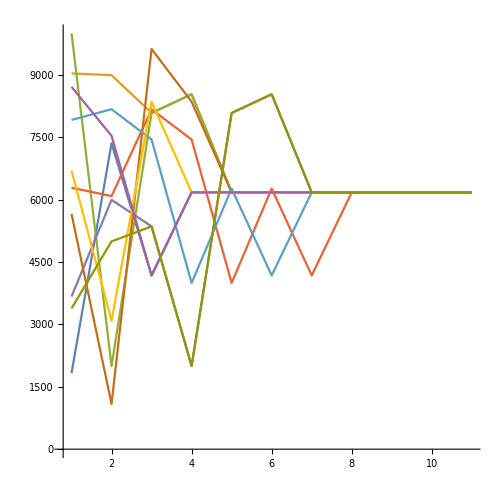

```mathematica
ListPlot[
Table[
NestList[Kaprekar[#,0]&,RandomInteger[{1001,9998}],10]
,{n,1,10}],PlotRange->All,
Joined->True,AspectRatio->1,ImageSize->500
]
```

```mathematica
iterLength=10;
alma=ParallelTable[Table[Module[
{nestlist},
nestlist=NestList[Kaprekar[#,j]&,i,iterLength];
If[
nestlist[[-1]]-nestlist[[-2]]==0,
Position[Differences[nestlist],0][[1]][[1]]/iterLength,
1
]
]
,{i,10000,10500}],{j,10000,10500}];
```

```mathematica
Export[NotebookDirectory[]<>"kaprekar.png",Image[alma]]
```

C:\Users\marku\Documents\CEU\hermann grid\human\granularity_effect\kaprekar.png